# de Broglie-Bohm pilot-wave description of double-slit experiment

Linearity of quantum dynamics implies consequences that contract our classical notions of nature.

Mohammad Bahrami, Jun. 24,  2018

Quantum theory, as the most successful theory invented so far, defies our classical picture of the world. At the heart of quantum mysteries is the interference experiments (e.g., the double-slit experiment as the archetype). The observation of interference pattern is usually interpreted as the wave nature of quantum systems; while its disappearance is usually considered as the fingerprint of particle features. The standard quantum theory does not provide

## Experimental parameters and physical constants

Our calculation is based on the double–slit experiment performed by Zeilinger et al. with cold neutrons. In this section, we will elaborate on the detail of experimental setup. Here, d is the gap between two slits, a1 is the width of the left slit, a2 is the width of the 2nd slit, x1 is the center of left slit, and likewise x2 is the center of the right slit. With a very good approximation, we assume that the diffracted wave function coming out of each slit can be described as a Gaussian wavepacket with the width σ which is set as 2(a1+a2). In this way, we are very sure that once coming out of slits, there is no overlap between two wave packets. The initial momentum of each wave packet is set as ℏ/a1 and -ℏ/a2, respectively. This means the left wavepacket is moving to the right with the momentum ℏ/a1 and the right one is moving to the left with the momentum -ℏ/a2. τ is the time that it takes for two wavepackets to meet again (say, overlap again). pz is the momentum of wavepackets along z-direction. We would assume that interference is happening along x-axis.

### The double-slit configuration of a double-slit experiment with neutrons

In the following, we represent the experimental configuration of the double-slit experiment

```mathematica
d=(5 104.1)/10^6;(*meter*)
a1=21.9*10^-6;(*left slit in meter*) 
a2=22.5*10^-6;(*right slit in meter*)
x1=-(a1+d)/2;(*the center of left slit*)
x2=(a2+d)/2;(*the center of right slit*)
σ=2(a1+a2);(*momentum along z-direction*)
τ=d/(ℏ/((a1+a2)/2)/m);(*the time that it takes two Gaussian along x-axis meet each other*)
pz=0.0001 √((h/λdB)^2-(ℏ/a1)^2);(*momentum along z-axis*)
```

### physical constants

```mathematica
c=QuantityMagnitude@UnitConvert[Quantity["SpeedOfLight"]];
eV=QuantityMagnitude@UnitConvert[Quantity["Electronvolts"]];
h=QuantityMagnitude@UnitConvert[Quantity["PlanckConstant"]];
ℏ=QuantityMagnitude@UnitConvert[Quantity["ReducedPlanckConstant"]];
m=QuantityMagnitude@UnitConvert[Quantity["NeutronMass"]];
λdB=h/(m*214.4);(*de Broghlie wavelength with velocity 214.4 m/s*)
```

## Wave functions as Gaussian wavepackets

In this part, we provide the detail formulas for Gaussian wavepackets and the superposition among them. Within the experimental conditions studied here, the spreading of the wavepackets can be neglected for all practical purposes.

The mathematical form of wavepackets, with σ the width, p the momentum, m the mass of particles, x0 the center of wavepacket

```mathematica
ψ[p_][x0_,x_][t_]:=(1/(2π σ^2))^(1/4)Exp[ⅈ/ℏ p x -(x-x0-(p t)/m )^2/(4 σ^2)];
```

The superposed wave function of two Gaussian wavepacets with the same weight (symmetric case)

```mathematica
ϕ[x_,t_]:=(ψ[ℏ/a1][x1,x][t]+ψ[-ℏ/a2][x2,x][t])/√2;
```

## Interference pattern along x-axis (axis of slits)

Here we plot the standard quantum interference at different times. The red line represents the wavepacket diffracted from the left slit and the green one is diffracted wavepacket from the right slit. The thick black line denotes the resulting interference pattern. Note that since there is no coupling for the movement along different directions in 3D, each direction is completely independent. The interference is happening along x-axis.

```mathematica
Manipulate[Plot[{Abs[#]^2&@ψ[ℏ/a1][x1,x][t],Abs[#]^2&@ψ[-ℏ/a2][x2,x][t],Abs[#]^2&@ϕ[x,t]},{x,-d,d},Frame->True,PlotRange->{All,{0,10000}},Filling->Automatic,PlotStyle->{{Red,Dashed},{Green,Dashed},{Black,Thick}},FrameTicks->{Automatic,None}],{t,0,τ}]
```

## Interference pattern along xz-axis (2D space where slit and detector are located)

To provide a more realistic description, here we included the movement of quantum system from slits to the detector plate as a function of time. The wavepackets moves with a constant momentum, selectively experimentally, toward the detector place along z-axis. Note that the motion along x-axis is independent from the motion along z-axis (no coupling).

```mathematica
ListAnimate@Table[Plot3D[Abs[ϕ[x,t] ψ[pz][0,z][t]]^2,{x,-d,d},{z,-d,8 d},PlotPoints->30,PlotRange->{0,3*10^7},Ticks->{All,All,None},Mesh->False],{t,0,τ,τ/10}]
```

## de Broglie-Bohm quantum trajectories

Add more sections as needed to explain the topic....

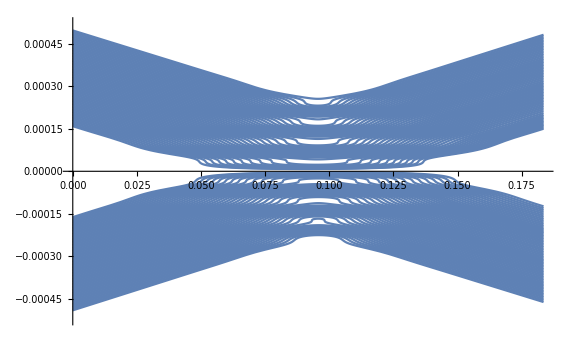

```mathematica
bohmTrajectory[q0_,tf_]:=Module[{ϕ,guidingDE,nde},
ϕ[x_,t_]:=ψ[ℏ/a1][x1,x][t]+ψ[-ℏ/a2][x2,x][t];
guidingDE=q'[t]==ℏ/m Im[Conjugate[ϕ[q[t],t]] D[ϕ[q[t],t],q[t]]]/(ϕ[q[t],t]Conjugate[ϕ[q[t],t]]);
nde=NDSolve[{guidingDE,q[0]==q0},q,{t,0,tf}];
Plot[Evaluate[q[t]/.nde],{t,0,tf},PlotRange->{All,{-d,d}},ImageSize->Large]]
Show[Table[bohmTrajectory[x2-5a2+i a2/4,τ],{i,0,60}],Table[bohmTrajectory[x1+5a1-i a1/4,τ],{i,0,60}]]
```

## Bohm quantum potential

Add more sections as needed to explain the topic....

```mathematica
conjψ[p_][x0_,x_][t_]:=(1/(2π σ^2))^(1/4)Exp[-ⅈ/ℏ p x -(x-x0-(p t)/m )^2/(4 σ^2)];
conjϕ[x_,t_]:=(conjψ[ℏ/a1][x1,x][t]+conjψ[-ℏ/a2][x2,x][t])/√2;
ρ[x_,t_]:=conjϕ[x,t] ϕ[x,t];
qQ[q_,t_]:=N[(-ℏ^2/(4m))/(10^-13 eV)((Derivative[2,0][ρ][q,t])/ρ[q,t]-1/2((Derivative[1,0][ρ][q,t])/ρ[q,t])^2)]//Re;
qQ2[q_,t_]=(-ℏ^2/(4m))/(10^-13 eV)((Derivative[2,0][ρ][q,t])/ρ[q,t]-1/2((Derivative[1,0][ρ][q,t])/ρ[q,t])^2);
Manipulate[Plot[qQ2[q,t],{q,0,d/5},PlotRange->{-3,1}],{t,τ/2-τ/5,τ/2+τ/5}]
Plot3D[qQ2[q,t],{q,-d/2,d/2},{t,τ/2-τ/5,τ/2+τ/5},PlotPoints->50,MaxRecursion->3,Mesh->None]
```

-Graphics3D-

## Further explorations

A. Zeilinger, R. Gahler, C.G. Shull, W. Treimer, and W. Mampe, Rev. Mod. Phys. 60, 1067 (1988).

## Author contact information

mbahram@calstatela.edu

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)